```mathematica
rssiValues=Import["~/Desktop/RSSI Values/Sheet 1-Table 2-1.csv"];
```

```mathematica
rssi1tile=rssiValues⟦3;;,2;;3⟧
```

{{75,77},{73,78},{73,67},{72,77},{73,78},{76,74},{66,78},{73,78},{66,74},{76,63},{72,74}}

```mathematica
rssi2tile=rssiValues⟦3;;,4;;5⟧
```

{{76,77},{78,80},{78,67},{75,80},{72,77},{72,67},{70,67},{67,76},{66,71},{71,69},{73,73}}

```mathematica
rssi3tile=rssiValues⟦3;;,6;;7⟧
```

{{73,76},{73,73},{73,73},{72,78},{69,77},{77,73},{78,77},{73,84},{77,74},{73,73},{74,76}}

```mathematica
rssi4tile=rssiValues⟦3;;,8;;9⟧
```

{{69,74},{74,77},{74,73},{73,77},{75,77},{78,74},{72,73},{70,74},{67,73},{73,74},{73,75}}

```mathematica
rssi5tile=rssiValues⟦3;;,10;;11⟧
```

{{77,79},{75,77},{75,78},{79,74},{72,73},{73,73},{72,73},{72,80},{73,74},{71,73},{74,75}}

```mathematica
rssi7tile=rssiValues⟦3;;,12;;13⟧
```

{{76,73},{74,78},{77,81},{77,77},{73,73},{81,77},{74,88},{78,78},{80,78},{80,77},{77,78}}

```mathematica
rssi9tile=rssiValues⟦3;;,14;;15⟧
```

{{74,80},{80,78},{74,83},{74,78},{78,79},{74,75},{74,78},{75,86},{75,78},{77,80},{76,80}}

```mathematica
rssi12tile=rssiValues⟦3;;,16;;17⟧
```

{{74,65},{78,71},{77,73},{72,73},{80,71},{74,79},{74,77},{64,77},{80,74},{73,68},{75,73}}

```mathematica
DiscretePlot[{{0.305,rssi1tile⟦1;;,1⟧},{0.305,rssi1tile⟦1;;,2⟧}}]
```

DiscretePlot::argr: DiscretePlot called with 1 argument; 2 arguments are expected.

DiscretePlot[{{0.305,rssi1tile⟦1;;All,1⟧},{0.305,rssi1tile⟦1;;All,2⟧}}]

```mathematica
Table[(x*0.305)/x,{x,1,12}]
```

{0.305,0.305,0.305,0.305,0.305,0.305,0.305,0.305,0.305,0.305,0.305,0.305}

```mathematica
Ratio[rssi_,calValOneMeter_]:=rssi/calValOneMeter;
```

```mathematica
Ratio[#,74.4]&/@rssi12tile⟦1;;,1⟧
```

{0.994624,1.04839,1.03495,0.967742,1.07527,0.994624,0.994624,0.860215,1.07527,0.981183,1.00806}

```mathematica
rssi1m=Import["~/Desktop/RSSI Values/Sheet 2-Table 1-1.csv"]
```

{{distance,Central mine strength,remote strength},{1 m,73,71},{,73,76},{,73,80},{,73,78},{,82,67},{,73,74},{,73,81},{,76,80},{,75,77},{0 degree remote,71,77}}

```mathematica
RemoteCurve[x_]:=-0.3303 x^2+3.2448x+72.194;
```

```mathematica
MineCurve[x_]:=-0.6819 x^2+3.7312x+70.767;
```

```mathematica
RemoteCurve[#]&/@rssi1m⟦2;;,2⟧
```

{-1451.1,-1451.1,-1451.1,-1451.1,-1882.67,-1451.1,-1451.1,-1589.01,-1542.38,-1362.47}

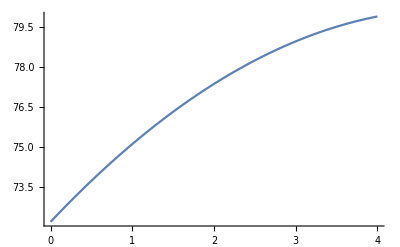

```mathematica
Plot[RemoteCurve[x],{x,0,4}]
```

```mathematica
BaseForm[Round[RemoteCurve[1]],16]
```

(4b)_16

For x < 0x4B ⇒ distance is less than 1m. And for x > 0x4B ⇒ distance is > 1m.